```mathematica
Quit[];(*2/3- 2 (Tanh[(x+4 t)])^2*)
```

```mathematica
u[x_,t_]:=2/3- 2 (Tanh[(x+4 t)])^2
```

```mathematica
u1=D[u[x,t],t]
```

-16 Sech[4 t+x]^2 Tanh[4 t+x]

```mathematica
u2=6 u[x,t] D[u[x,t],x]
```

-24 Sech[4 t+x]^2 Tanh[4 t+x] (2/3-2 Tanh[4 t+x]^2)

```mathematica
u3=D[D[D[u[x,t],x],x],x]
```

32 Sech[4 t+x]^4 Tanh[4 t+x]-16 Sech[4 t+x]^2 Tanh[4 t+x]^3

```mathematica
uu=u1+u2+u3
```

-16 Sech[4 t+x]^2 Tanh[4 t+x]+32 Sech[4 t+x]^4 Tanh[4 t+x]-16 Sech[4 t+x]^2 Tanh[4 t+x]^3-24 Sech[4 t+x]^2 Tanh[4 t+x] (2/3-2 Tanh[4 t+x]^2)

```mathematica
Simplify[uu]
```

0

```mathematica
Plot3D[u[x,t],{x,-1,1},{t,-1,1}]
```

-Graphics3D-

```mathematica
Quit[];
```

```mathematica
(*initial value 2/3 ;0 ;-4*)
```

```mathematica
2/3- 2 (Tanh[0])^2
```

2/3

```mathematica
D[2/3- 2 (Tanh[x])^2,x]
```

-4 Sech[x]^2 Tanh[x]

```mathematica
q1[x_]:=-4 Sech[x]^2 Tanh[x];
```

```mathematica
q1[0]
```

0

```mathematica
D[q1[x],x]
```

-4 Sech[x]^4+8 Sech[x]^2 Tanh[x]^2

```mathematica
q2[x_]:=-4 Sech[x]^4+8 Sech[x]^2 Tanh[x]^2;
```

```mathematica
q2[0]
```

-4

```mathematica
Quit[];
```

```mathematica
s=NDSolve[{X'[t] == Y[t],
Y'[t]==Z[t],Z'[t]==-4 Y[t]-6 X[t] Y[t], 
X[0]==2/3,Y[0]==0,Z[0]==-4},{X[t],Y[t],Z[t]},{t,-3,3}]
```

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t]}}

```mathematica
Table[X[t]/.s,{t,-3,3}]
```

{{-1.3136},{-1.19203},{-0.493385},{0.666667},{-0.493385},{-1.19203},{-1.3136}}

```mathematica
Table[Y[t]/.s,{t,-3,3}]
```

{{0.0392682},{0.272437},{1.2794},{0.},{-1.2794},{-0.272437},{-0.0392682}}

```mathematica
Table[Z[t]/.s,{t,-3,3}]
```

{{0.0777618},{0.505308},{1.24325},{-4.},{1.24325},{0.505308},{0.0777618}}

```mathematica
ss=DSolve[{X'[t] == Y[t],
Y'[t]==Z[t],Z'[t]==-4 Y[t],
X[0]==2/3,Y[0]==0,Z[0]==-4},{X[t],Y[t],Z[t]},{t,-3,3}]
```

{{X[t]→-1/3+Cos[2 t],Y[t]→-2 Sin[2 t],Z[t]→-4 Cos[2 t]}}

```mathematica
sol=Simplify[ExpToTrig[ss]]
```

{{X[t]→-1/3+Cos[2 t],Y[t]→-2 Sin[2 t],Z[t]→-4 Cos[2 t]}}

```mathematica
Plot[{Evaluate[X[t]/.sol],2/3- 2 (Tanh[t])^2},{t,-1,1},PlotRange->All,PlotStyle->{{Red,Dashed,Thick},{Green,DotDashed,Thick}},PlotLabels->{"(ū)_1","u"},Frame->True]
```

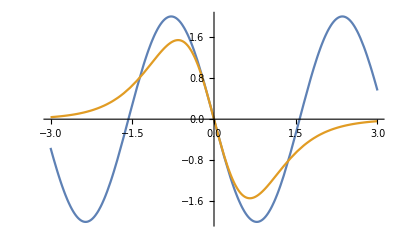

```mathematica
Plot[{Evaluate[Y[t]/.sol],-4 Sech[t]^2 Tanh[t]},{t,-3,3},PlotRange->All]
```

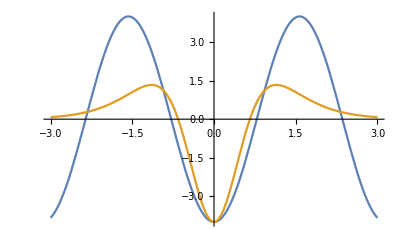

```mathematica
Plot[{Evaluate[Z[t]/.sol],-4 Sech[t]^4+8 Sech[t]^2 Tanh[t]^2},{t,-3,3},PlotRange->All]
```